MIT License
Copyright (c) 2021 Gaetana Spedalieri  gae.spedalieri@york.ac.uk

Permission is hereby granted, free of charge, to any person obtaining a copy of this software and associated documentation files (the “Software”), to deal in the Software without restriction,including without limitation the rights to use, copy, modify, merge, publish, distribute, sublicense, and/or sell copies of the Software, and to permit persons to whom the Software is furnished to do so,subject to the following conditions: The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,  FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM, OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.

```mathematica
Quit[]
```

```mathematica
(* parameters *)
```

```mathematica
pfaNUM=N[10^-3];
SNRdBNUM=-20;
NbNUM = 600;
mNUM = 5000;
NmaNUM=100; (* truncation for third-moment sums *)
```

```mathematica
SNR[SNRdB_]:=10^(SNRdB/10)
Fepsilon[pfa_]:=N[InverseCDF[NormalDistribution[0,1],pfa]]
```

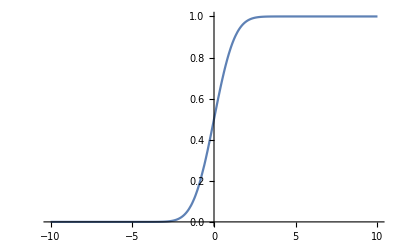

```mathematica
Plot[CDF[NormalDistribution[0,1],pfa],{pfa,-10,10}]
```

```mathematica
N[Fepsilon[pfaNUM]]
N[√2 InverseErf[2 pfaNUM-1]]
```

-3.09023

-3.09023

```mathematica
(* Marcum *)
```

```mathematica
marcum[m_,SNR_,pfa_]:=1-MarcumQ[1,√(2 m SNR),√(-2 Log[pfa])]
marcumdB[m_,SNRdB_,pfa_]:=1-MarcumQ[1,√(2 m SNR[SNRdB]),√(-2 Log[pfa])]
marcumNs[m_,pfa_,k_,Ns_,Nb_]:=1-MarcumQ[1,√(2 m (k Ns)/Nb),√(-2 Log[pfa])]
```

```mathematica
Relative[Ns_,Nb_,k_]:=k Ns Log[1 + 1/Nb]
RelVariance[Ns_,Nb_,k_]:=k Ns (2 Nb + 1)(Log[1 + 1/Nb])^2
RelativeSNR[SNR_,Nb_]:=SNR Nb Log[1 + 1/Nb]
RelVarianceSNR[SNR_,Nb_]:=SNR Nb (2 Nb + 1)(Log[1 + 1/Nb])^2
```

```mathematica
Series[Relative[Ns,Nb,k],{Nb,∞,1}]
Series[RelVariance[Ns,Nb,k],{Nb,∞,1}]
```

(k Ns)/Nb+O[1/Nb]^2

(2 k Ns)/Nb+O[1/Nb]^2

```mathematica
TypeII[m_,Nb_,SNRdB_]:=Exp[-m  SNR[SNRdB] Nb Log[1 + 1/Nb] ]
```

```mathematica
exponentIIorder[Nb_,SNRdB_]:= SNR[SNRdB] Nb Log[1 + 1/Nb]
```

```mathematica
(* valid for large background *)
AsyTypeII[m_,SNRdB_]:=Exp[-m  SNR[SNRdB] ]
```

```mathematica
γ[x_,nB_]:=nB^x/(nB+1)^(x+1)
```

```mathematica
ThirdM2[nS_,nB_,η_,Nma_]:=Exp[- η nS]    ∑_(k=0)^Nma ∑_(l=0)^Nma ((l!)/(k!) (η nS)^(k-l)   LaguerreL[l,k-l,η nS]^2   γ[k,nB]  Abs[(k-l-η nS) Log[nB/(nB+1)]]^3)
```

```mathematica
(***** set η nS = SNR Nb  ***)
```

```mathematica
ThirdMsnr[SNR_,nB_,Nma_]:=Exp[- SNR nB]    ∑_(k=0)^Nma ∑_(l=0)^Nma ((l!)/(k!) (SNR nB)^(k-l)   LaguerreL[l,k-l,SNR nB]^2   γ[k,nB]  Abs[(k-l-SNR nB) Log[nB/(nB+1)]]^3)
ThirdMsnrDB[SNRdB_,nB_,Nma_]:=ThirdMsnr[SNR[SNRdB],nB,Nma]
```

```mathematica
Block[{$MaxExtraPrecision=1000},N[ThirdMsnrDB[-10,10,NmaNUM],10]]
```

0.1718276239

```mathematica
(***** Conditions Ke Li  ****)
```

```mathematica
cNUM=0.4748;
```

```mathematica
condL[Nb_,SNR_,pfa_,m_,Nma_]:=pfa+1/(√m)( (cNUM ThirdMsnr[SNR,Nb,Nma])/RelVarianceSNR[SNR,Nb]^(3/2)+2)  (* must be ≤1 *)
condU[Nb_,SNR_,pfa_,m_,Nma_]:=pfa-1/(√m) (cNUM ThirdMsnr[SNR,Nb,Nma])/RelVarianceSNR[SNR,Nb]^(3/2) (* must be ≥0 *)
condLdB[Nb_,SNRdB_,pfa_,m_,Nma_]:=condL[Nb,SNR[SNRdB],pfa,m,Nma]
condUdB[Nb_,SNRdB_,pfa_,m_,Nma_]:=condU[Nb,SNR[SNRdB],pfa,m,Nma]
```

```mathematica
TypeIILBexact[Nb_,SNRdB_,pfa_,m_,Nma_]:=Exp[-m  SNR[SNRdB] Nb  Log[1 + 1/Nb]- √(m SNR[SNRdB] Nb (2 Nb + 1)(Log[1 + 1/Nb])^2)Fepsilon[condLdB[Nb,SNRdB,pfa,m,Nma]]]/(2^9 m^2)
TypeIIUBexact[Nb_,SNRdB_,pfa_,m_,Nma_]:=Exp[-m  SNR[SNRdB] Nb  Log[1 + 1/Nb]- √(m SNR[SNRdB] Nb (2 Nb + 1)(Log[1 + 1/Nb])^2)Fepsilon[condUdB[Nb,SNRdB,pfa,m,Nma]]]
```

```mathematica
(*  error exponent - log [] / m  *)
```

```mathematica
ExponentLB[Nb_,SNRdB_,pfa_,m_,Nma_]:=(m  SNR[SNRdB] Nb  Log[1 + 1/Nb]+ √(m SNR[SNRdB] Nb (2 Nb + 1)(Log[1 + 1/Nb])^2)Fepsilon[condLdB[Nb,SNRdB,pfa,m,Nma]])/m+Log[2^9 m^2]/m
ExponentUB[Nb_,SNRdB_,pfa_,m_,Nma_]:=(m  SNR[SNRdB] Nb  Log[1 + 1/Nb]+ √(m SNR[SNRdB] Nb (2 Nb + 1)(Log[1 + 1/Nb])^2)Fepsilon[condUdB[Nb,SNRdB,pfa,m,Nma]])/m
```

```mathematica
(* refresh of some of the parameters *)
```

```mathematica
pfaNUM=N[10^-3];
SNRdBNUM=-35;  (* test value *)
NbNUM = 600;
mNUM = 5000;
```

```mathematica
Print["conditions"]
Block[{$MaxExtraPrecision=1000},N[condLdB[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],10]] (* must be ≤1 *)
Block[{$MaxExtraPrecision=1000},N[condUdB[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],10]] (* must be ≥0 *)
Print["probs"]
Block[{$MaxExtraPrecision=1000},N[TypeIILBexact[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],100]]
Block[{$MaxExtraPrecision=1000},N[TypeIIUBexact[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],100]]
N[TypeII[mNUM,NbNUM,SNRdBNUM]]
Block[{$MaxExtraPrecision=1000},N[marcumdB[mNUM,SNRdBNUM,pfaNUM],100]]
Print["exponents"]
Block[{$MaxExtraPrecision=1000},N[ExponentLB[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],100]]
(* Max[Block[{$MaxExtraPrecision=1000},N[ExponentUB[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],100]],0] *)
Block[{$MaxExtraPrecision=1000},N[ExponentUB[NbNUM,SNRdBNUM,pfaNUM,mNUM,NmaNUM],100]]
N[exponentIIorder[NbNUM,SNRdBNUM]]
Block[{$MaxExtraPrecision=1000},N[(-Log[marcumdB[mNUM,SNRdBNUM,pfaNUM]])/mNUM,100]]
```

conditions

0.0292972

0.000987062

probs

4.64152×10^-10

50.4033

0.206012

0.959404

exponents

0.00429816

-0.000784012

0.000315965

8.28851×10^-6

```mathematica
(* Data collection *)
```

```mathematica
ListaExponentUB=Table[{SNRdB,Block[{$MaxExtraPrecision=1000},N[ExponentUB[NbNUM,SNRdB,pfaNUM,mNUM,NmaNUM],100]]},{SNRdB,-33,-21,2}]
```

{{-33,-0.000884353},{-31,-0.000950673},{-29,-0.000939075},{-27,-0.000773184},{-25,-0.000323131},{-23,0.00062373},{-21,0.00241835}}

```mathematica
ListaExponentUB2={{-35,-0.0007840115252505767},{-33,-0.0008843527240085772},{-31,-0.0009506730652697055},{-30,-0.000959888288736684},{-29,-0.0009390748626411199},{-28,-0.0008820665441049371},{-27,-0.0007731838872466786},{-26,-0.0005944260588713434},{-25,-0.0003231309244504665},{-24,0.00007027437953172609},{-23,0.0006237295532774049},{-22,0.0013857676944797426},{-21,0.0024183498456419776},{-20,0.003800455163075111}};
```

```mathematica
ListaExponentLB=Table[{SNRdB,Block[{$MaxExtraPrecision=1000},N[ExponentLB[NbNUM,SNRdB,pfaNUM,mNUM,NmaNUM],100]]},{SNRdB,-33,-21,2}]
```

{{-33,0.0043089},{-31,0.00438266},{-29,0.00457102},{-27,0.00495948},{-25,0.00568826},{-23,0.00698583},{-21,0.00922177}}

```mathematica
ListaExponentLB2={{-35,0.004298161643718417},{-33,0.0043088966030792415},{-31,0.004382663575721155},{-30,0.0044582404007277605},{-29,0.004571024587477551},{-28,0.004733076619887994},{-27,0.004959475891402673},{-26,0.005269613333267512},{-25,0.005688261114093708},{-24,0.00624695872543583},{-23,0.006985830972558204},{-22,0.00795586334851519},{-21,0.009221771769597976},{-20,0.010865621871235697}};
```

```mathematica
ListaexponentIIorder= Table[{SNRdB,N[exponentIIorder[NbNUM,SNRdB]]},{SNRdB,-35,-20,1}];
```

```mathematica
ListaMarcum= Table[{SNRdB,Block[{$MaxExtraPrecision=1000},N[(-Log[marcumdB[mNUM,SNRdB,pfaNUM]])/mNUM,100]]},{SNRdB,-35,-20,1}];
```

```mathematica
(* PLOTs *)
```

```mathematica
pic1=ListPlot[ListaExponentUB2,Joined->True,PlotRange->All,PlotStyle->Red];
pic2=ListPlot[ListaExponentLB2,Joined->True,PlotRange->All,PlotStyle->Red];
```

```mathematica
(* Show[pic1,pic2,PlotRange->All,Frame->True] *)
```

```mathematica
pic3=ListPlot[ListaexponentIIorder,Joined->True,PlotRange->All,PlotStyle->Black];
pic4=ListPlot[ListaMarcum,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}];
```

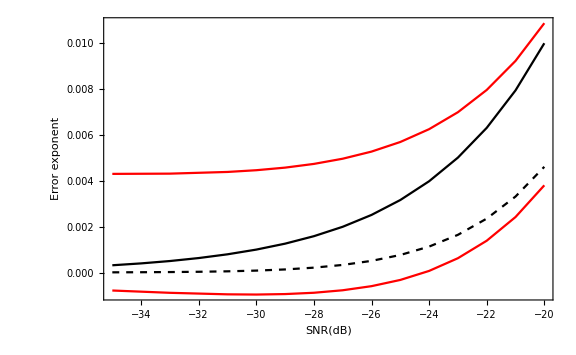

```mathematica
Show[pic1,pic2,pic3,pic4,PlotRange->All,Frame->True,AxesOrigin->{-20,-0.001},FrameLabel->{{"Error exponent",""},{"SNR(dB)",""}},ImageSize->Large,LabelStyle->{FontSize->14}]
```

```mathematica
(******* ADDITIONAL ******)
```

```mathematica
(* check truncation for the selected range  *)
```

```mathematica
NmaNUM4=400;
NmaNUM5=500;
```

```mathematica
Block[{$MaxExtraPrecision=1000},N[condLdB[NbNUM,-35,pfaNUM,mNUM,NmaNUM4],10]] (* must be ≤1 *)
Block[{$MaxExtraPrecision=1000},N[condUdB[NbNUM,-35,pfaNUM,mNUM,NmaNUM4],10]] (* must be ≥0 *)
```

0.0292972

0.000987062

```mathematica
Block[{$MaxExtraPrecision=1000},N[condLdB[NbNUM,-35,pfaNUM,mNUM,NmaNUM5],10]] (* must be ≤1 *)
Block[{$MaxExtraPrecision=1000},N[condUdB[NbNUM,-35,pfaNUM,mNUM,NmaNUM5],10]] (* must be ≥0 *)
```

$Aborted

$Aborted

```mathematica
Block[{$MaxExtraPrecision=1000},N[condLdB[NbNUM,-20,pfaNUM,mNUM,NmaNUM4],10]] (* must be ≤1 *)
Block[{$MaxExtraPrecision=1000},N[condUdB[NbNUM,-20,pfaNUM,mNUM,NmaNUM4],10]] (* must be ≥0 *)
```

0.0298975

0.000386795

```mathematica
Block[{$MaxExtraPrecision=1000},N[condLdB[NbNUM,-20,pfaNUM,mNUM,NmaNUM5],10]] (* must be ≤1 *)
Block[{$MaxExtraPrecision=1000},N[condUdB[NbNUM,-20,pfaNUM,mNUM,NmaNUM5],10]] (* must be ≥0 *)
```

0.0302684

0.0000158298